## Init, Start

```mathematica
<<MultiAgent`
<<MultiAgent`
```

```mathematica
?initMultiAgentExchange
initMultiAgentExchange[]
```

Function for initialising Multi Agent system (Mono/Multi)

{Days→30,NumberOfProducts→5,AgentsAmount→10,StartMoney→10,ProdFuncInd→1,SessionsInDay→2,FirstPrice→{1,2},FromFile→DefaultTestFile,SystemType→Mono}

```mathematica
?runExchange
agentGoods /@ agentsNums;
runExchange[]
productsNames
hAgentsLastDay
```

main function that runs MAExchange

{Money,Labor,Water,Energy,Ferrum}

{∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}

## Input Params

```mathematica
?printAgentParams
printAgentParams/@agentsNums;
```

prints all agent parameters: id, prod/cons, norm, prodfunc, etc.

***** [1] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {1.15,0.00,0.00,0.00,0.00}

Daily regen: {0.00,2.61,1.60,2.29,0.00}

Start store: {9.98,0.00,1.68,10.38,0.00}

Consume norm: 0.53

Lambda coef: 0.58

***** [2] Agent Parameters *****

Produces good: 3, Water

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {1.95,0.00,0.00,0.00,0.00}

Daily regen: {0.80,0.86,0.82,1.04,2.86}

Start store: {3.09,0.00,11.10,0.00,11.79}

Consume norm: 0.54

Lambda coef: 0.61

***** [3] Agent Parameters *****

Produces good: 1, Money

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,1.53,0.00,0.00,0.00}

Daily regen: {2.73,0.00,2.04,0.00,0.00}

Start store: {15.54,17.91,1.94,0.00,0.00}

Consume norm: 0.44

Lambda coef: 0.47

***** [4] Agent Parameters *****

Produces good: 5, Ferrum

Consumed good: 4, Energy

Production function: 1

Func coefs : {1.36,0.00,0.00,0.00,0.00}

Daily regen: {2.00,0.54,0.00,0.66,2.81}

Start store: {3.77,0.00,0.00,16.63,18.56}

Consume norm: 0.59

Lambda coef: 0.23

***** [5] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {2.00,0.00,0.00,0.00,0.00}

Daily regen: {1.49,0.00,1.26,0.00,0.00}

Start store: {16.73,0.00,12.37,13.36,0.00}

Consume norm: 0.53

Lambda coef: 0.56

***** [6] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.00,1.41,0.00,0.00}

Daily regen: {2.65,1.45,1.44,0.00,1.24}

Start store: {6.87,0.00,5.55,13.17,0.00}

Consume norm: 0.58

Lambda coef: 0.52

***** [7] Agent Parameters *****

Produces good: 4, Energy

Consumed good: 3, Water

Production function: 1

Func coefs : {0.00,0.00,1.32,0.00,0.00}

Daily regen: {0.00,1.07,0.10,0.18,2.35}

Start store: {17.04,0.00,0.50,15.87,0.00}

Consume norm: 0.45

Lambda coef: 0.77

***** [8] Agent Parameters *****

Produces good: 3, Water

Consumed good: 4, Energy

Production function: 1

Func coefs : {0.00,0.00,0.00,1.37,0.00}

Daily regen: {2.32,0.90,0.00,0.71,2.68}

Start store: {2.65,0.00,10.21,8.02,0.00}

Consume norm: 0.45

Lambda coef: 0.29

***** [9] Agent Parameters *****

Produces good: 1, Money

Consumed good: 2, Labor

Production function: 1

Func coefs : {0.00,0.00,0.00,0.00,1.80}

Daily regen: {0.00,0.00,1.16,0.88,1.22}

Start store: {10.14,10.84,0.00,0.00,11.33}

Consume norm: 0.56

Lambda coef: 0.50

***** [10] Agent Parameters *****

Produces good: 1, Money

Consumed good: 5, Ferrum

Production function: 1

Func coefs : {0.00,0.00,1.91,0.00,0.00}

Daily regen: {0.00,0.00,0.00,0.44,2.95}

Start store: {17.59,0.00,17.29,0.00,2.76}

Consume norm: 0.53

Lambda coef: 0.37

## Agents

[an]: Shows how (an)-agent main curency is changing

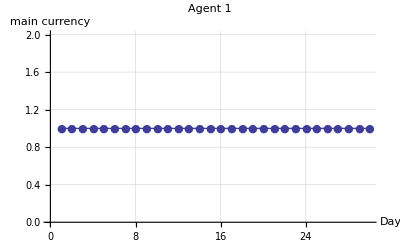
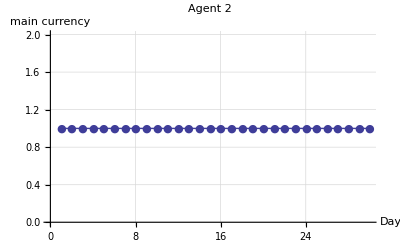
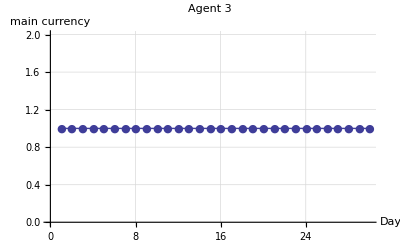
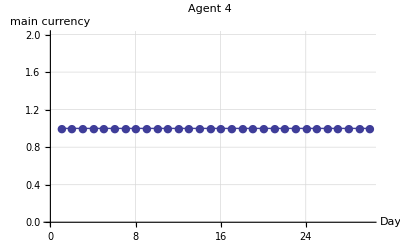
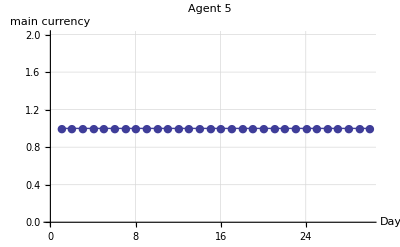
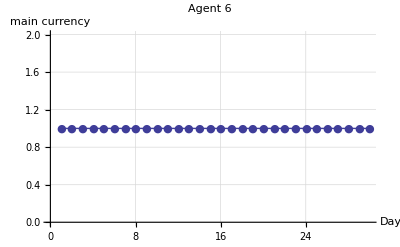
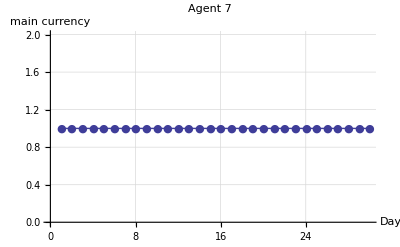
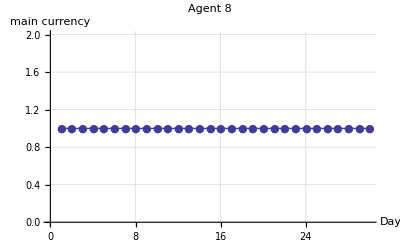

[an]: Shows all production of (an)-agent

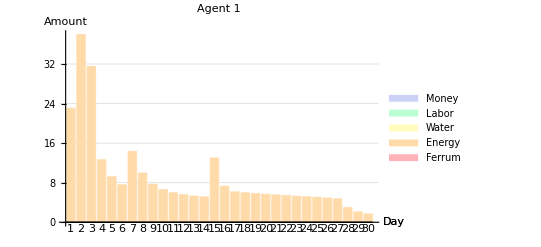
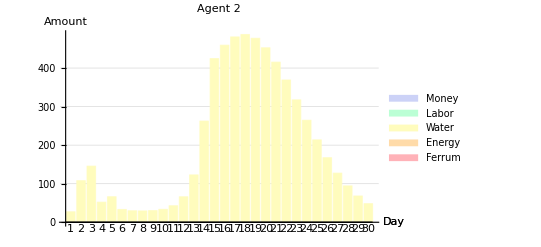
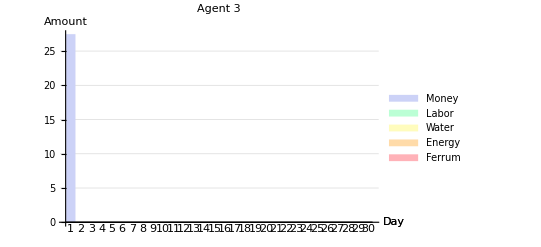
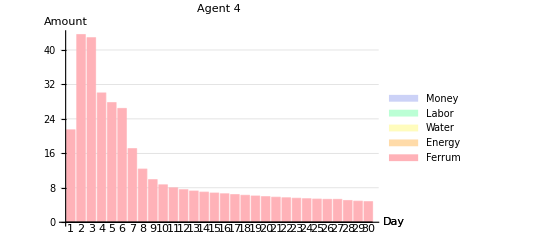
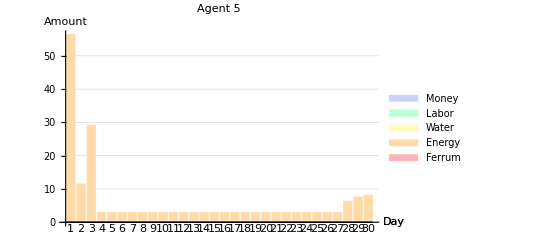
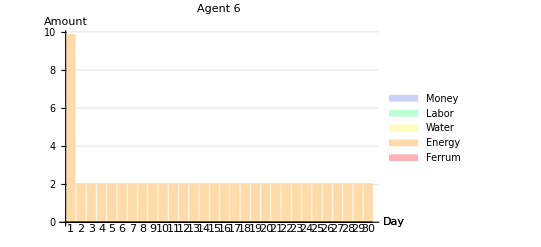
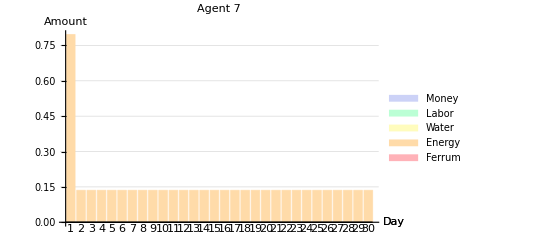
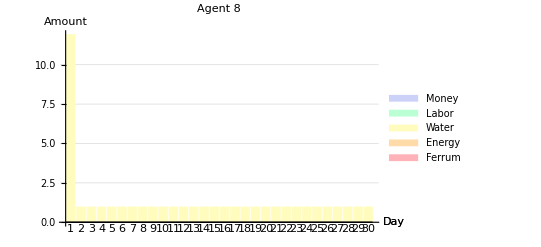

[an]: Shows all consumption of (an)-agent

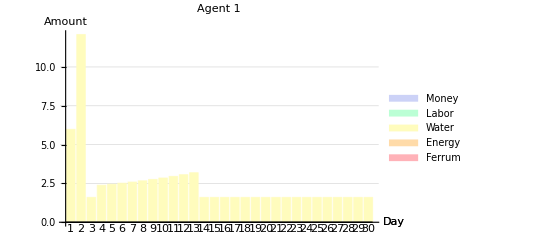
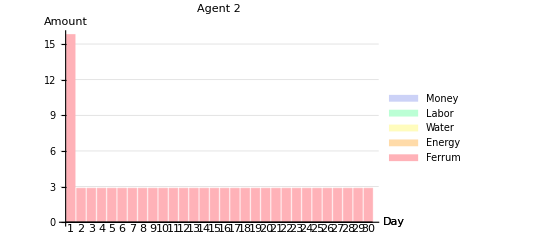
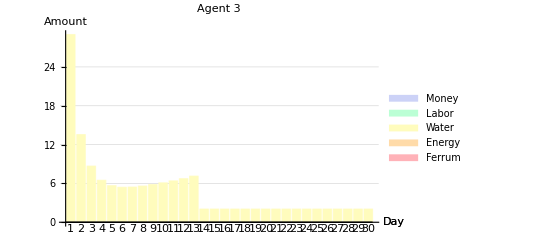
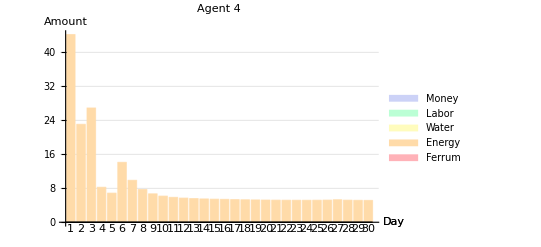
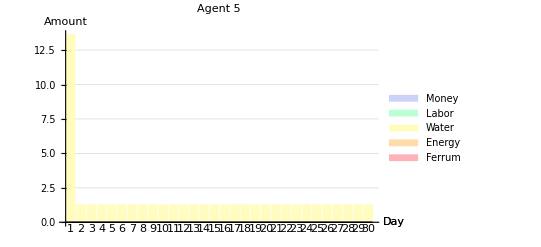
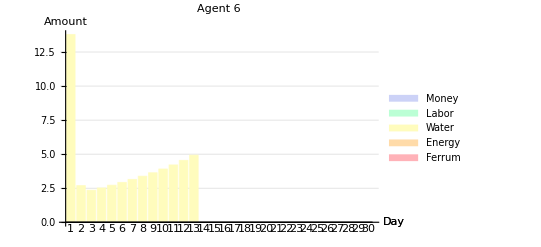
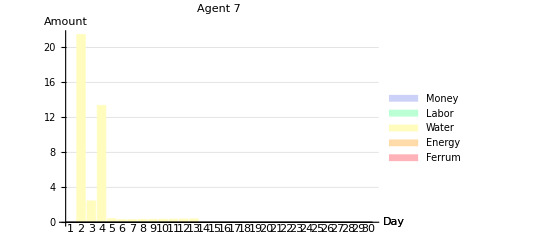
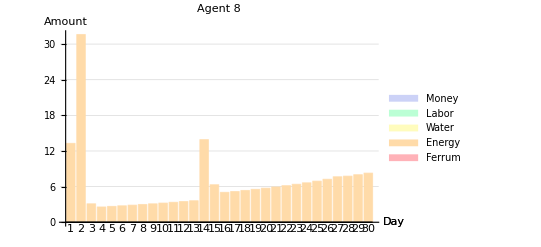

[an]: Shows how (an)-agent portfolio cost is changing

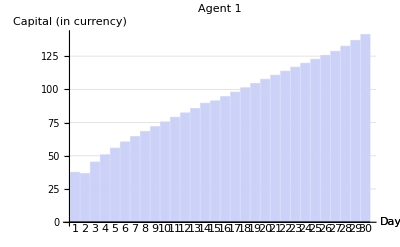
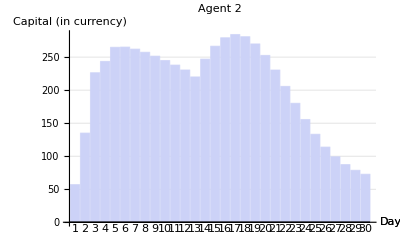
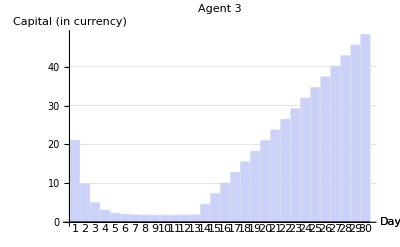
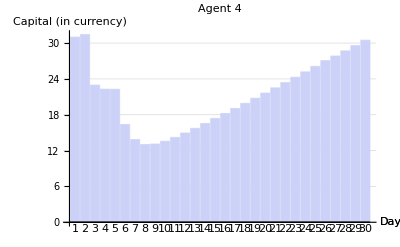
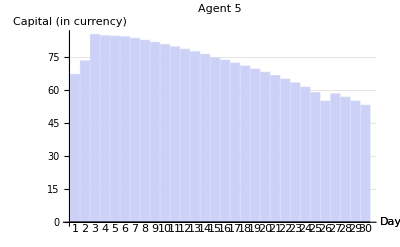
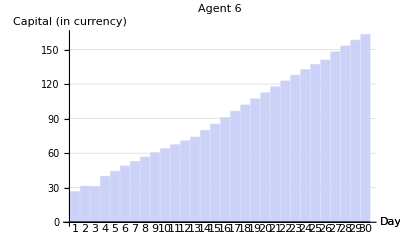
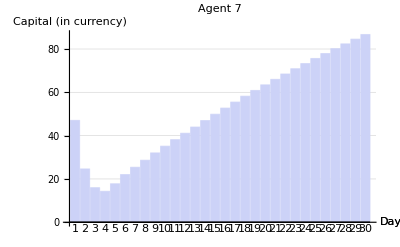
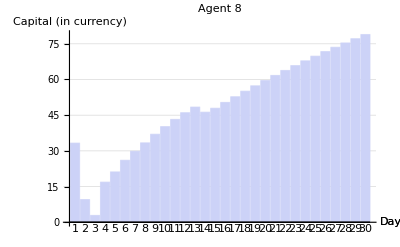

[pc]: Shows (pc)richest to (pc)poorest ratio

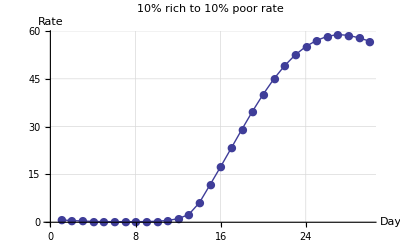

[bn]: Shows histogram of agents' richness with (bn) beans

[an]: Shows (an)-agent storage, claculated in it's main currency

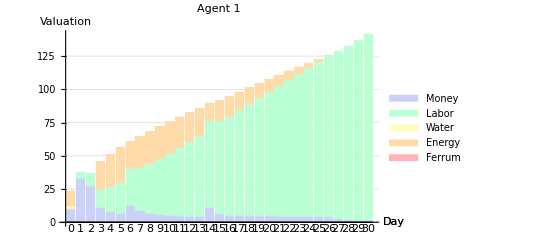
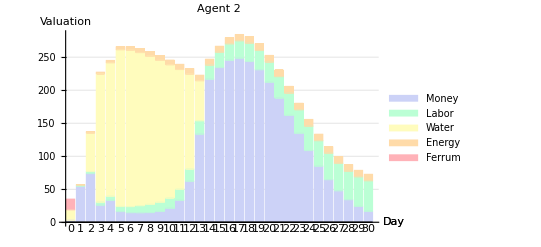
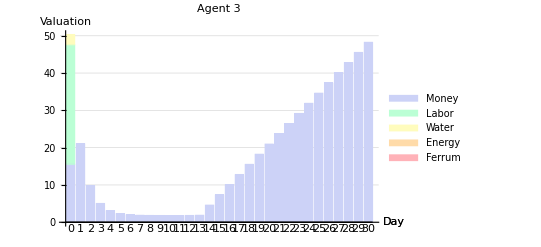
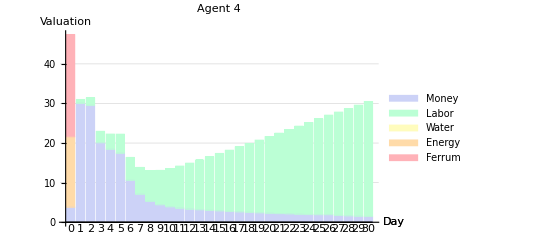
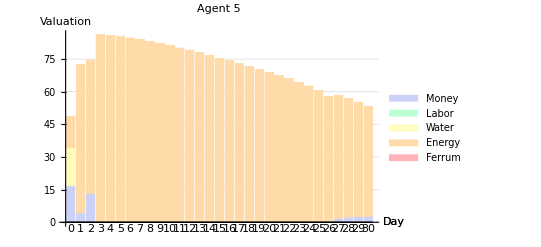
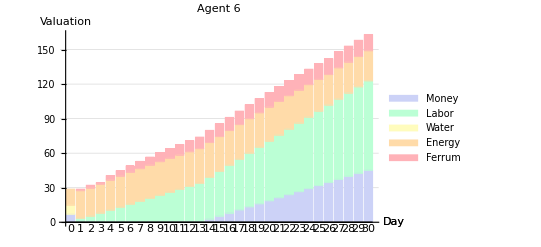
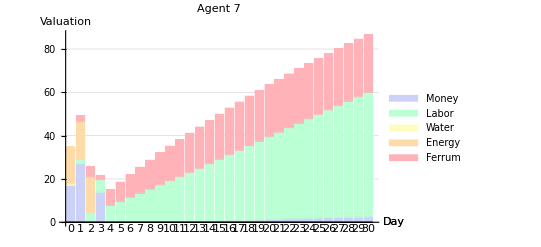
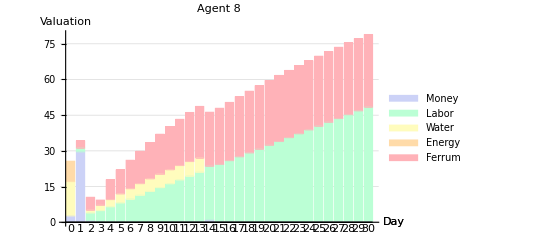

```mathematica
?MAEVisAgentCurrency
MAEVisAgentCurrency /@agentsNums

?MAEVisAgentProduce
MAEVisAgentProduce/@agentsNums

?MAEVisAgentConsume
MAEVisAgentConsume/@agentsNums

?MAEVisAgentCapital
MAEVisAgentCapital /@agentsNums

?MAEVisAgentsDifference
MAEVisAgentsDifference[10]

?MAEVisAgentsHistogram
MAEVisAgentsHistogram[10]

?MAEVisAgentProducts
MAEVisAgentProducts /@ agentsNums
```

```mathematica
?MAEVisAgentActionsTable
MAEVisAgentActionsTable /@ {1,10}
```

[an]: Table of all actions by (an)-agent

{DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 9.98 Money
1.68 Water
10.38 Energy
1/1 | 23.06 Energy | m3: {Ask 35.73Ene x 1.07Mon} | m3: [S]12.70Ene/14.28Mon | 5.98 Water | 32.88 Money
2.61 Labor
1/2 |  | m2: {Bid 5.30Wat x 1.42Mon}
m3: {Ask 23.03Ene x 0.74Mon} | m2: [B]2.70Wat/3.60Mon
m3: [S]23.03Ene/22.20Mon |  | 
2/1 | 37.96 Energy | m3: {Ask 40.25Ene x 0.84Mon} | m3: [S]27.98Ene/27.76Mon | 12.09 Water | 27.29 Money
5.21 Labor
2/2 |  | m2: {Bid 10.49Wat x 1.39Mon}
m3: {Ask 12.26Ene x 0.36Mon} | m2: [B]10.49Wat/12.19Mon
m3: [S]12.26Ene/11.71Mon |  | 
3/1 | 31.50 Energy | m3: {Ask 33.79Ene x 0.81Mon} | --- | 1.60 Water | 10.96 Money
7.82 Labor
21.94 Energy
3/2 |  | m3: {Ask 33.79Ene x 0.81Mon} | m3: [S]11.84Ene/10.96Mon |  | 
4/1 | 12.65 Energy | m3: {Ask 36.88Ene x 0.77Mon} | m3: [S]1.96Ene/1.78Mon | 2.38 Water | 7.97 Money
10.43 Labor
27.06 Energy
4/2 |  | m2: {Bid 0.78Wat x 1.19Mon}
m3: {Ask 34.92Ene x 0.76Mon} | m2: [B]0.78Wat/0.81Mon
m3: [S]7.86Ene/7.00Mon |  | 
5/1 | 9.20 Energy | m3: {Ask 38.55Ene x 0.74Mon} | m3: [S]2.04Ene/1.78Mon | 2.44 Water | 6.56 Money
13.03 Labor
30.01 Energy
5/2 |  | m2: {Bid 0.84Wat x 1.11Mon}
m3: {Ask 36.51Ene x 0.73Mon} | m2: [B]0.84Wat/0.82Mon
m3: [S]6.50Ene/5.60Mon |  | 
6/1 | 7.57 Energy | m3: {Ask 39.87Ene x 0.71Mon} | m3: [S]2.13Ene/1.79Mon | 2.51 Water | 12.43 Money
15.64 Labor
23.99 Energy
6/2 |  | m2: {Bid 0.91Wat x 1.03Mon}
m3: {Ask 37.74Ene x 0.70Mon} | m2: [B]0.91Wat/0.82Mon
m3: [S]13.75Ene/11.46Mon |  | 
7/1 | 14.35 Energy | m3: {Ask 40.62Ene x 0.69Mon} | m3: [S]2.23Ene/1.80Mon | 2.59 Water | 8.62 Money
18.25 Labor
28.86 Energy
7/2 |  | m2: {Bid 0.99Wat x 0.96Mon}
m3: {Ask 38.39Ene x 0.68Mon} | m2: [B]0.99Wat/0.83Mon
m3: [S]9.53Ene/7.65Mon |  | 
8/1 | 9.95 Energy | m3: {Ask 41.10Ene x 0.66Mon} | m3: [S]2.33Ene/1.81Mon | 2.67 Water | 6.68 Money
20.86 Labor
31.39 Energy
8/2 |  | m2: {Bid 1.07Wat x 0.89Mon}
m3: {Ask 38.77Ene x 0.65Mon} | m2: [B]1.07Wat/0.83Mon
m3: [S]7.38Ene/5.70Mon |  | 
9/1 | 7.71 Energy | m3: {Ask 41.39Ene x 0.64Mon} | m3: [S]2.43Ene/1.82Mon | 2.75 Water | 5.72 Money
23.46 Labor
32.58 Energy
9/2 |  | m2: {Bid 1.15Wat x 0.83Mon}
m3: {Ask 38.96Ene x 0.63Mon} | m2: [B]1.15Wat/0.84Mon
m3: [S]6.38Ene/4.74Mon |  | 
10/1 | 6.60 Energy | m3: {Ask 41.47Ene x 0.61Mon} | m3: [S]2.54Ene/1.83Mon | 2.85 Water | 5.17 Money
26.07 Labor
33.08 Energy
10/2 |  | m2: {Bid 1.25Wat x 0.77Mon}
m3: {Ask 38.93Ene x 0.60Mon} | m2: [B]1.25Wat/0.84Mon
m3: [S]5.86Ene/4.19Mon |  | 
11/1 | 5.97 Energy | m3: {Ask 41.34Ene x 0.59Mon} | m3: [S]2.65Ene/1.84Mon | 2.95 Water | 4.83 Money
28.68 Labor
33.11 Energy
11/2 |  | m2: {Bid 1.35Wat x 0.72Mon}
m3: {Ask 38.68Ene x 0.58Mon} | m2: [B]1.35Wat/0.84Mon
m3: [S]5.58Ene/3.83Mon |  | 
12/1 | 5.58 Energy | m3: {Ask 40.97Ene x 0.57Mon} | m3: [S]2.77Ene/1.84Mon | 3.06 Water | 4.60 Money
31.28 Labor
32.78 Energy
12/2 |  | m2: {Bid 1.46Wat x 0.66Mon}
m3: {Ask 38.20Ene x 0.56Mon} | m2: [B]1.46Wat/0.83Mon
m3: [S]5.42Ene/3.58Mon |  | 
13/1 | 5.31 Energy | m3: {Ask 40.38Ene x 0.55Mon} | m3: [S]2.89Ene/1.85Mon | 3.19 Water | 4.45 Money
33.89 Labor
32.16 Energy
13/2 |  | m2: {Bid 1.59Wat x 0.61Mon}
m3: {Ask 37.48Ene x 0.54Mon} | m2: [B]1.59Wat/0.78Mon
m3: [S]5.32Ene/3.38Mon |  | 
14/1 | 5.14 Energy | m3: {Ask 39.59Ene x 0.53Mon} | m3: [S]3.02Ene/1.86Mon | 1.60 Water | 11.27 Money
36.50 Labor
21.17 Energy
14/2 |  | m2: {Bid 1.76Wat x 0.56Mon}
m3: {Ask 36.57Ene x 0.51Mon} | m3: [S]15.40Ene/9.41Mon |  | 
15/1 | 13.01 Energy | m3: {Ask 36.47Ene x 0.51Mon} | m3: [S]4.58Ene/2.72Mon | 1.60 Water | 6.32 Money
39.10 Labor
25.70 Energy
15/2 |  | m2: {Bid 2.53Wat x 0.56Mon}
m3: {Ask 31.88Ene x 0.49Mon} | m3: [S]6.18Ene/3.61Mon |  | 
16/1 | 7.30 Energy | m3: {Ask 35.29Ene x 0.49Mon} | m3: [S]3.44Ene/1.96Mon | 1.60 Water | 5.33 Money
41.71 Labor
25.86 Energy
16/2 |  | m2: {Bid 1.85Wat x 0.56Mon}
m3: {Ask 31.85Ene x 0.47Mon} | m3: [S]6.00Ene/3.37Mon |  | 
17/1 | 6.16 Energy | m3: {Ask 34.30Ene x 0.47Mon} | m3: [S]3.56Ene/1.95Mon | 1.60 Water | 5.17 Money
44.32 Labor
24.78 Energy
17/2 |  | m2: {Bid 1.88Wat x 0.54Mon}
m3: {Ask 30.74Ene x 0.45Mon} | m3: [S]5.97Ene/3.23Mon |  | 
18/1 | 5.97 Energy | m3: {Ask 33.04Ene x 0.45Mon} | m3: [S]3.71Ene/1.95Mon | 1.60 Water | 5.04 Money
46.92 Labor
23.38 Energy
18/2 |  | m2: {Bid 1.95Wat x 0.53Mon}
m3: {Ask 29.33Ene x 0.43Mon} | m3: [S]5.95Ene/3.09Mon |  | 
19/1 | 5.82 Energy | m3: {Ask 31.48Ene x 0.43Mon} | m3: [S]3.87Ene/1.96Mon | 1.60 Water | 4.91 Money
49.53 Labor
21.67 Energy
19/2 |  | m2: {Bid 2.01Wat x 0.51Mon}
m3: {Ask 27.61Ene x 0.42Mon} | m3: [S]5.94Ene/2.96Mon |  | 
20/1 | 5.67 Energy | m3: {Ask 29.64Ene x 0.41Mon} | m3: [S]4.04Ene/1.96Mon | 1.60 Water | 4.80 Money
52.14 Labor
19.66 Energy
20/2 |  | m2: {Bid 2.08Wat x 0.49Mon}
m3: {Ask 25.60Ene x 0.40Mon} | m3: [S]5.94Ene/2.84Mon |  | 
21/1 | 5.54 Energy | m3: {Ask 27.49Ene x 0.40Mon} | m3: [S]4.22Ene/1.97Mon | 1.60 Water | 4.69 Money
54.75 Labor
17.33 Energy
21/2 |  | m2: {Bid 2.16Wat x 0.48Mon}
m3: {Ask 23.27Ene x 0.38Mon} | m3: [S]5.94Ene/2.72Mon |  | 
22/1 | 5.41 Energy | m3: {Ask 25.02Ene x 0.38Mon} | m3: [S]4.40Ene/1.97Mon | 1.60 Water | 4.58 Money
57.35 Labor
14.66 Energy
22/2 |  | m2: {Bid 2.24Wat x 0.46Mon}
m3: {Ask 20.62Ene x 0.36Mon} | m3: [S]5.96Ene/2.61Mon |  | 
23/1 | 5.28 Energy | m3: {Ask 22.24Ene x 0.37Mon} | m3: [S]4.60Ene/1.98Mon | 1.60 Water | 4.47 Money
59.96 Labor
11.66 Energy
23/2 |  | m2: {Bid 2.32Wat x 0.45Mon}
m3: {Ask 17.64Ene x 0.34Mon} | m3: [S]5.98Ene/2.50Mon |  | 
24/1 | 5.16 Energy | m3: {Ask 19.11Ene x 0.35Mon} | m3: [S]4.81Ene/1.98Mon | 1.60 Water | 4.37 Money
62.57 Labor
8.28 Energy
24/2 |  | m2: {Bid 2.40Wat x 0.43Mon}
m3: {Ask 14.29Ene x 0.32Mon} | m3: [S]6.01Ene/2.39Mon |  | 
25/1 | 5.04 Energy | m3: {Ask 15.61Ene x 0.33Mon} | m3: [S]5.05Ene/1.99Mon | 1.60 Water | 4.26 Money
65.17 Labor
4.50 Energy
25/2 |  | m2: {Bid 2.49Wat x 0.42Mon}
m3: {Ask 10.56Ene x 0.29Mon} | m3: [S]6.07Ene/2.27Mon |  | 
26/1 | 4.92 Energy | m3: {Ask 11.70Ene x 0.32Mon} | m3: [S]5.31Ene/2.00Mon | 1.60 Water | 4.11 Money
67.78 Labor
0.24 Energy
26/2 |  | m2: {Bid 2.59Wat x 0.41Mon}
m3: {Ask 6.39Ene x 0.25Mon} | m3: [S]6.15Ene/2.11Mon |  | 
27/1 | 4.74 Energy | m3: {Ask 7.27Ene x 0.30Mon} | m3: [S]5.66Ene/2.02Mon | 1.60 Water | 2.59 Money
70.39 Labor
27/2 |  | m2: {Bid 2.70Wat x 0.39Mon}
m3: {Ask 1.61Ene x 0.04Mon} | m3: [S]1.61Ene/0.57Mon |  | 
28/1 | 2.99 Energy | m3: {Ask 5.28Ene x 0.29Mon} | m3: [S]5.28Ene/1.82Mon | 1.60 Water | 1.82 Money
72.99 Labor
28/2 |  | m2: {Bid 2.52Wat x 0.38Mon} | --- |  | 
29/1 | 2.10 Energy | m3: {Ask 4.39Ene x 0.28Mon} | m3: [S]4.39Ene/1.46Mon | 1.60 Water | 1.46 Money
75.60 Labor
29/2 |  | m2: {Bid 2.08Wat x 0.37Mon} | --- |  | 
30/1 | 1.68 Energy | m3: {Ask 3.97Ene x 0.27Mon} | m3: [S]3.97Ene/1.27Mon | 1.60 Water | 1.27 Money
78.21 Labor
30/2 |  | m2: {Bid 1.88Wat x 0.36Mon} | --- |  |  
Agent 1,DAY/SES | Produce | Orders | Deals | Consume | Storage After All
0 | --- | --- | --- | --- | 17.59 Money
17.29 Water
2.76 Ferrum
1/1 | 33.09 Money | m2: {Bid 18.43Wat x 1.56Mon}
m4: {Bid 20.89Fer x 1.53Mon} | m2: [B]18.43Wat/26.10Mon
m4: [B]20.89Fer/30.52Mon | 28.00 Ferrum | 1.34 Money
19.67 Water
0.44 Energy
1/2 |  | m2: {Bid 1.23Wat x 1.56Mon}
m4: {Bid 1.40Fer x 1.53Mon} | m2: [B]1.23Wat/1.64Mon
m4: [B]1.40Fer/1.08Mon |  | 
2/1 | 37.65 Money | m2: {Bid 12.38Wat x 1.49Mon}
m4: {Bid 14.89Fer x 1.38Mon} | m2: [B]12.38Wat/15.44Mon
m4: [B]14.89Fer/17.76Mon | 20.05 Ferrum | 1.79 Money
14.21 Water
0.88 Energy
2/2 |  | m2: {Bid 1.84Wat x 1.49Mon}
m4: {Bid 2.21Fer x 1.38Mon} | m2: [B]1.84Wat/2.13Mon
m4: [B]2.21Fer/1.86Mon |  | 
3/1 | 27.21 Money | m2: {Bid 9.90Wat x 1.39Mon}
m4: {Bid 12.25Fer x 1.25Mon} | m2: [B]9.90Wat/11.23Mon
m4: [B]12.25Fer/13.32Mon | 17.08 Ferrum | 3.73 Money
11.42 Water
1.32 Energy
3/2 |  | m2: {Bid 1.52Wat x 1.39Mon}
m4: {Bid 1.88Fer x 1.25Mon} | m2: [B]1.52Wat/1.70Mon
m4: [B]1.88Fer/0.98Mon |  | 
4/1 | 21.86 Money | m2: {Bid 9.37Wat x 1.29Mon}
m4: {Bid 15.08Fer x 0.89Mon} | m2: [B]9.37Wat/9.87Mon
m4: [B]15.08Fer/12.97Mon | 19.65 Ferrum | 0.59 Money
10.38 Water
1.76 Energy
4/2 |  | m2: {Bid 1.01Wat x 1.29Mon}
m4: {Bid 1.62Fer x 0.89Mon} | m2: [B]1.01Wat/1.04Mon
m4: [B]1.62Fer/1.11Mon |  | 
5/1 | 19.87 Money | m2: {Bid 8.06Wat x 1.20Mon}
m4: {Bid 12.69Fer x 0.85Mon} | m2: [B]8.06Wat/7.86Mon
m4: [B]12.69Fer/10.33Mon | 17.04 Ferrum | 0.43 Money
8.95 Water
2.20 Energy
5/2 |  | m2: {Bid 0.89Wat x 1.20Mon}
m4: {Bid 1.41Fer x 0.85Mon} | m2: [B]0.89Wat/0.87Mon
m4: [B]1.41Fer/0.98Mon |  | 
6/1 | 17.13 Money | m2: {Bid 7.43Wat x 1.12Mon}
m4: {Bid 11.36Fer x 0.81Mon} | m2: [B]7.43Wat/6.74Mon
m4: [B]11.36Fer/8.45Mon | 14.31 Ferrum | 1.46 Money
8.43 Water
2.64 Energy
6/2 |  | m2: {Bid 1.00Wat x 1.12Mon}
m4: {Bid 1.53Fer x 0.81Mon} | m2: [B]1.00Wat/0.90Mon |  | 
7/1 | 16.14 Money | m2: {Bid 8.01Wat x 1.04Mon}
m4: {Bid 11.75Fer x 0.79Mon} | m2: [B]8.01Wat/6.76Mon
m4: [B]11.75Fer/8.54Mon | 14.70 Ferrum | 1.43 Money
9.06 Water
3.08 Energy
7/2 |  | m2: {Bid 1.05Wat x 1.04Mon}
m4: {Bid 1.54Fer x 0.79Mon} | m2: [B]1.05Wat/0.88Mon |  | 
8/1 | 17.34 Money | m2: {Bid 9.18Wat x 0.97Mon}
m4: {Bid 12.90Fer x 0.77Mon} | m2: [B]9.18Wat/7.20Mon
m4: [B]12.90Fer/9.12Mon | 15.85 Ferrum | 1.51 Money
10.37 Water
3.52 Energy
8/2 |  | m2: {Bid 1.19Wat x 0.97Mon}
m4: {Bid 1.68Fer x 0.77Mon} | m2: [B]1.19Wat/0.93Mon |  | 
9/1 | 19.85 Money | m2: {Bid 11.23Wat x 0.90Mon}
m4: {Bid 15.12Fer x 0.74Mon} | m2: [B]11.23Wat/8.20Mon
m4: [B]12.71Fer/8.86Mon | 15.65 Ferrum | 2.66 Money
13.50 Water
3.96 Energy
9/2 |  | m2: {Bid 2.26Wat x 0.90Mon}
m4: {Bid 3.05Fer x 0.74Mon} | m2: [B]2.26Wat/1.64Mon |  | 
10/1 | 25.84 Money | m2: {Bid 16.12Wat x 0.84Mon}
m4: {Bid 20.65Fer x 0.73Mon} | m2: [B]16.12Wat/10.93Mon
m4: [B]11.50Fer/7.80Mon | 14.45 Ferrum | 6.05 Money
21.64 Water
4.40 Energy
10/2 |  | m2: {Bid 5.52Wat x 0.84Mon}
m4: {Bid 7.07Fer x 0.73Mon} | m2: [B]5.52Wat/3.72Mon |  | 
11/1 | 41.43 Money | m2: {Bid 28.89Wat x 0.78Mon}
m4: {Bid 35.26Fer x 0.71Mon} | m2: [B]28.89Wat/18.20Mon
m4: [B]10.81Fer/7.13Mon | 13.76 Ferrum | 13.77 Money
42.36 Water
4.84 Energy
11/2 |  | m2: {Bid 13.48Wat x 0.78Mon}
m4: {Bid 16.45Fer x 0.71Mon} | m2: [B]13.48Wat/8.38Mon |  | 
12/1 | 81.10 Money | m2: {Bid 62.16Wat x 0.72Mon}
m4: {Bid 72.32Fer x 0.69Mon} | m2: [B]62.16Wat/36.32Mon
m4: [B]10.37Fer/6.65Mon | 13.32 Ferrum | 32.57 Money
96.16 Water
5.28 Energy
12/2 |  | m2: {Bid 34.00Wat x 0.72Mon}
m4: {Bid 39.56Fer x 0.69Mon} | m2: [B]34.00Wat/19.33Mon |  | 
13/1 | 184.09 Money | m2: {Bid 153.27Wat x 0.67Mon}
m4: {Bid 169.67Fer x 0.67Mon} | m2: [B]153.27Wat/82.68Mon
m4: [B]10.06Fer/6.26Mon | 13.01 Ferrum | 83.15 Money
243.62 Water
5.72 Energy
13/2 |  | m2: {Bid 90.35Wat x 0.67Mon}
m4: {Bid 100.02Fer x 0.67Mon} | m2: [B]90.35Wat/44.56Mon |  | 
14/1 | 466.38 Money | m2: {Bid 424.17Wat x 0.61Mon}
m4: {Bid 442.39Fer x 0.65Mon} | m2: [B]393.11Wat/223.61Mon
m4: [B]9.81Fer/5.93Mon | 12.76 Ferrum | 319.99 Money
393.11 Water
6.16 Energy
14/2 |  | m2: {Bid 246.99Wat x 0.61Mon}
m4: {Bid 257.61Fer x 0.65Mon} | --- |  | 
15/1 | 752.56 Money | m2: {Bid 850.30Wat x 0.60Mon}
m4: {Bid 887.98Fer x 0.64Mon} | m2: [B]426.30Wat/234.75Mon
m4: [B]9.59Fer/5.64Mon | 12.54 Ferrum | 832.17 Money
426.30 Water
6.60 Energy
15/2 |  | m2: {Bid 659.73Wat x 0.60Mon}
m4: {Bid 688.96Fer x 0.64Mon} | --- |  | 
16/1 | 816.10 Money | m2: {Bid 1344.78Wat x 0.58Mon}
m4: {Bid 1403.87Fer x 0.62Mon} | m2: [B]461.05Wat/245.72Mon
m4: [B]9.42Fer/5.38Mon | 12.37 Ferrum | 1397.17 Money
461.05 Water
7.04 Energy
16/2 |  | m2: {Bid 1139.92Wat x 0.58Mon}
m4: {Bid 1190.00Fer x 0.62Mon} | --- |  | 
17/1 | 882.61 Money | m2: {Bid 1916.84Wat x 0.56Mon}
m4: {Bid 1998.08Fer x 0.60Mon} | m2: [B]482.52Wat/248.85Mon
m4: [B]9.23Fer/5.12Mon | 12.18 Ferrum | 2025.80 Money
482.52 Water
7.48 Energy
17/2 |  | m2: {Bid 1703.30Wat x 0.56Mon}
m4: {Bid 1775.48Fer x 0.60Mon} | --- |  | 
18/1 | 923.72 Money | m2: {Bid 2558.16Wat x 0.55Mon}
m4: {Bid 2660.52Fer x 0.58Mon} | m2: [B]488.68Wat/243.86Mon
m4: [B]9.06Fer/4.88Mon | 12.01 Ferrum | 2700.78 Money
488.68 Water
7.92 Energy
18/2 |  | m2: {Bid 2342.42Wat x 0.55Mon}
m4: {Bid 2436.15Fer x 0.58Mon} | --- |  | 
19/1 | 935.51 Money | m2: {Bid 3255.40Wat x 0.53Mon}
m4: {Bid 3376.18Fer x 0.57Mon} | m2: [B]478.95Wat/231.23Mon
m4: [B]8.90Fer/4.66Mon | 11.85 Ferrum | 3400.40 Money
478.95 Water
8.36 Energy
19/2 |  | m2: {Bid 3044.22Wat x 0.53Mon}
m4: {Bid 3157.16Fer x 0.57Mon} | --- |  | 
20/1 | 916.88 Money | m2: {Bid 3991.42Wat x 0.51Mon}
m4: {Bid 4126.38Fer x 0.55Mon} | m2: [B]454.31Wat/212.20Mon
m4: [B]8.76Fer/4.45Mon | 11.71 Ferrum | 4100.63 Money
454.31 Water
8.80 Energy
20/2 |  | m2: {Bid 3791.12Wat x 0.51Mon}
m4: {Bid 3919.32Fer x 0.55Mon} | --- |  | 
21/1 | 869.72 Money | m2: {Bid 4746.95Wat x 0.50Mon}
m4: {Bid 4890.67Fer x 0.54Mon} | m2: [B]417.14Wat/188.48Mon
m4: [B]8.62Fer/4.25Mon | 11.57 Ferrum | 4777.61 Money
417.14 Water
9.24 Energy
21/2 |  | m2: {Bid 4562.87Wat x 0.50Mon}
m4: {Bid 4701.02Fer x 0.54Mon} | --- |  | 
22/1 | 798.55 Money | m2: {Bid 5502.65Wat x 0.48Mon}
m4: {Bid 5648.85Fer x 0.52Mon} | m2: [B]370.83Wat/162.09Mon
m4: [B]8.49Fer/4.07Mon | 11.44 Ferrum | 5410.00 Money
370.83 Water
9.68 Energy
22/2 |  | m2: {Bid 5338.68Wat x 0.48Mon}
m4: {Bid 5480.53Fer x 0.52Mon} | --- |  | 
23/1 | 709.89 Money | m2: {Bid 6241.04Wat x 0.46Mon}
m4: {Bid 6383.04Fer x 0.51Mon} | m2: [B]319.28Wat/135.00Mon
m4: [B]8.38Fer/3.90Mon | 11.33 Ferrum | 5980.99 Money
319.28 Water
10.12 Energy
23/2 |  | m2: {Bid 6099.39Wat x 0.46Mon}
m4: {Bid 6238.17Fer x 0.51Mon} | --- |  | 
24/1 | 611.21 Money | m2: {Bid 6948.13Wat x 0.45Mon}
m4: {Bid 7079.21Fer x 0.49Mon} | m2: [B]266.37Wat/108.95Mon
m4: [B]8.27Fer/3.74Mon | 11.22 Ferrum | 6479.51 Money
266.37 Water
10.56 Energy
24/2 |  | m2: {Bid 6829.35Wat x 0.45Mon}
m4: {Bid 6958.19Fer x 0.49Mon} | --- |  | 
25/1 | 509.92 Money | m2: {Bid 7614.42Wat x 0.43Mon}
m4: {Bid 7728.13Fer x 0.48Mon} | m2: [B]215.48Wat/85.26Mon
m4: [B]8.18Fer/3.59Mon | 11.13 Ferrum | 6900.58 Money
215.48 Water
11.00 Energy
25/2 |  | m2: {Bid 7517.62Wat x 0.43Mon}
m4: {Bid 7629.89Fer x 0.48Mon} | --- |  | 
26/1 | 412.51 Money | m2: {Bid 8235.25Wat x 0.42Mon}
m4: {Bid 8325.66Fer x 0.46Mon} | m2: [B]169.21Wat/64.76Mon
m4: [B]8.12Fer/3.46Mon | 11.07 Ferrum | 7244.87 Money
169.21 Water
11.44 Energy
26/2 |  | m2: {Bid 8158.42Wat x 0.42Mon}
m4: {Bid 8247.99Fer x 0.46Mon} | --- |  | 
27/1 | 323.93 Money | m2: {Bid 8810.48Wat x 0.41Mon}
m4: {Bid 8872.24Fer x 0.45Mon} | m2: [B]129.18Wat/47.83Mon
m4: [B]8.12Fer/3.36Mon | 11.07 Ferrum | 7517.61 Money
129.18 Water
11.88 Energy
27/2 |  | m2: {Bid 8750.89Wat x 0.41Mon}
m4: {Bid 8812.24Fer x 0.45Mon} | --- |  | 
28/1 | 247.30 Money | m2: {Bid 9343.67Wat x 0.39Mon}
m4: {Bid 9372.07Fer x 0.44Mon} | m2: [B]96.11Wat/34.42Mon
m4: [B]7.85Fer/3.16Mon | 10.80 Ferrum | 7727.33 Money
96.11 Water
12.32 Energy
28/2 |  | m2: {Bid 9298.45Wat x 0.39Mon}
m4: {Bid 9326.71Fer x 0.44Mon} | --- |  | 
29/1 | 183.99 Money | m2: {Bid 9841.16Wat x 0.38Mon}
m4: {Bid 9832.02Fer x 0.42Mon} | m2: [B]69.93Wat/24.23Mon
m4: [B]7.70Fer/3.01Mon | 10.65 Ferrum | 7884.08 Money
69.93 Water
12.76 Energy
29/2 |  | m2: {Bid 9807.28Wat x 0.38Mon}
m4: {Bid 9798.17Fer x 0.42Mon} | --- |  | 
30/1 | 133.87 Money | m2: {Bid 10310.60Wat x 0.37Mon}
m4: {Bid 10260.20Fer x 0.41Mon} | m2: [B]50.03Wat/16.77Mon
m4: [B]7.60Fer/2.88Mon | 10.54 Ferrum | 7998.31 Money
50.03 Water
13.20 Energy
30/2 |  | m2: {Bid 10285.30Wat x 0.37Mon}
m4: {Bid 10235.00Fer x 0.41Mon} | --- |  |  
Agent 10}

## Goods

[pn]: Shows amount of producers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows amount of consumers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows daily production of (pn)-good

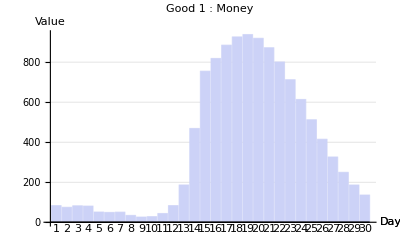
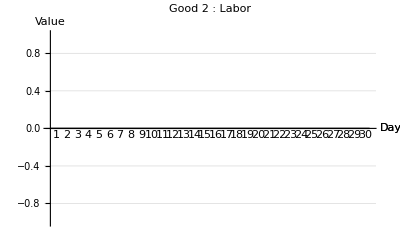
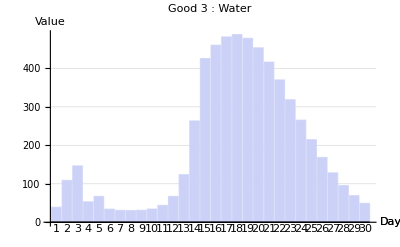
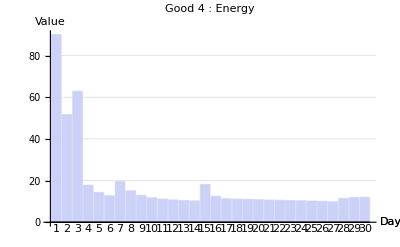
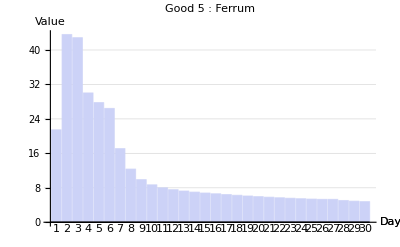

[pn]: Shows daily consumption of (pn)-good

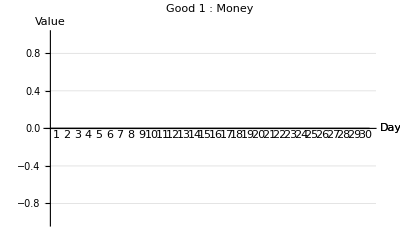
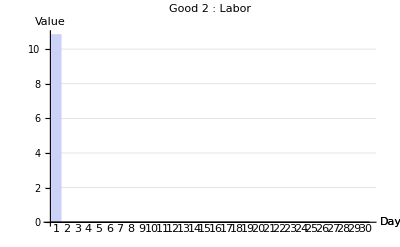
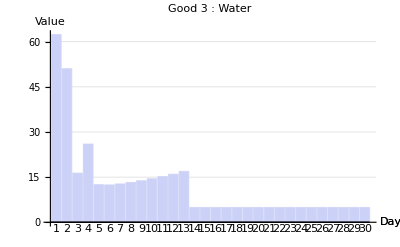
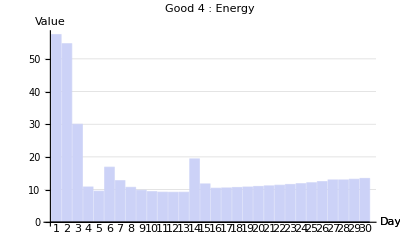
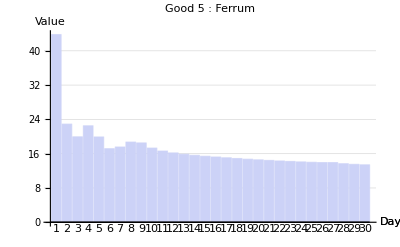

[pn]: Shows average production of (pn)-good (total prod a day / prod agents number)

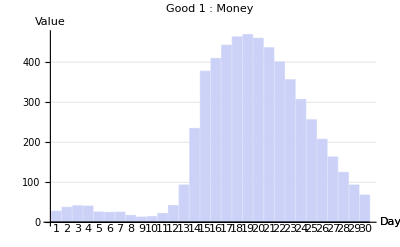
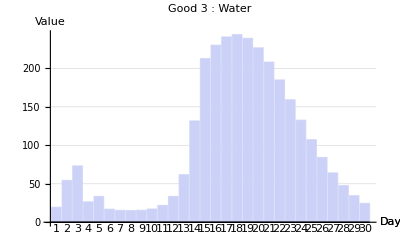
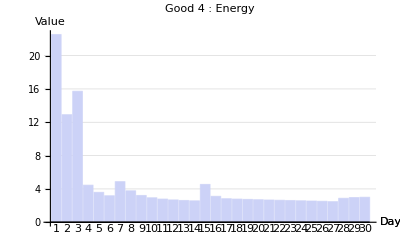
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows average consumption of (pn)-good (total cons a day / cons agents number)

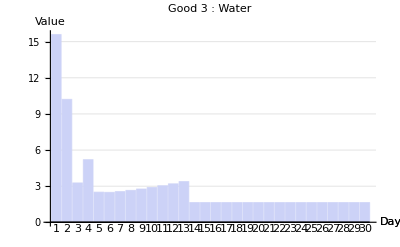
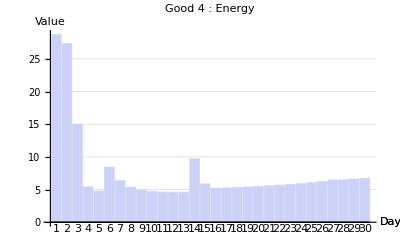
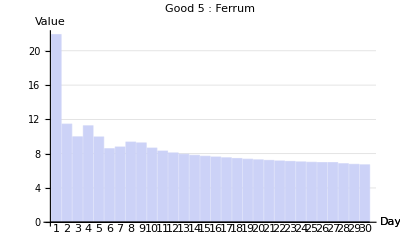
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows cumulative production of (pn)-good

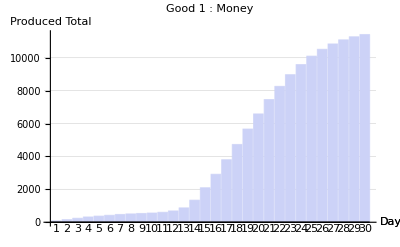
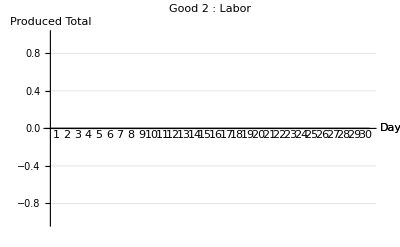
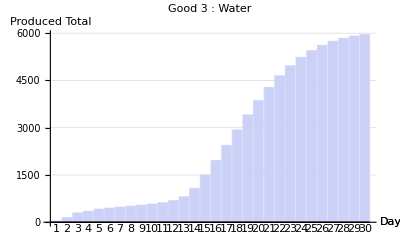
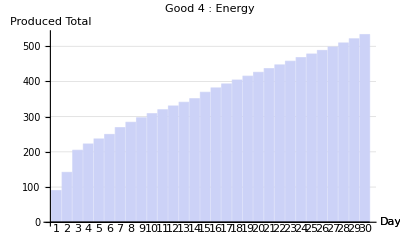
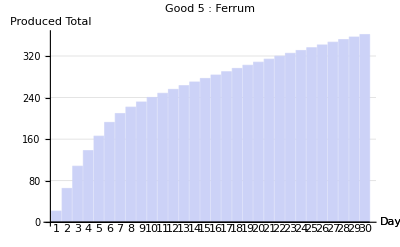

[pn]: Shows cumulative consumption of (pn)-good

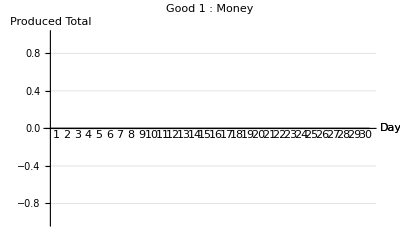
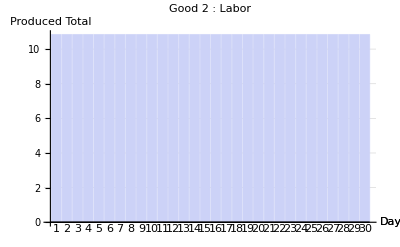
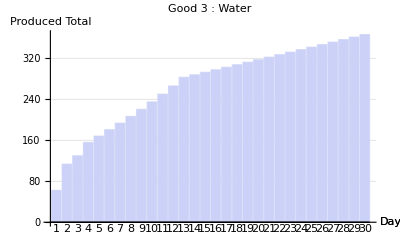
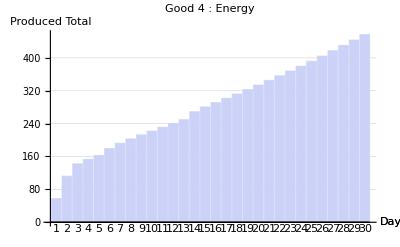
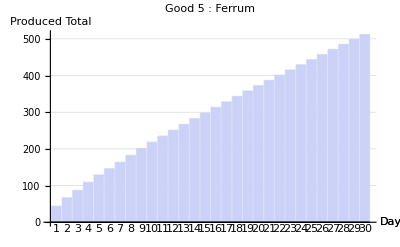

[pn]: Shows (pn)-good storage dynamics by agents

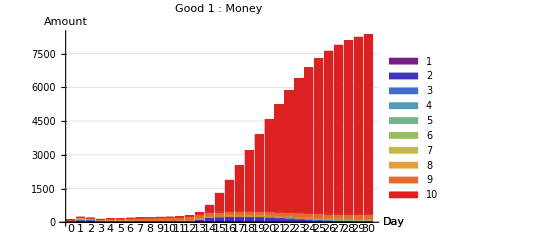
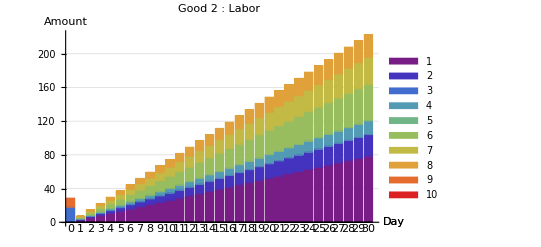
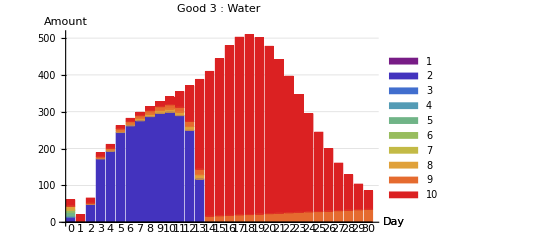
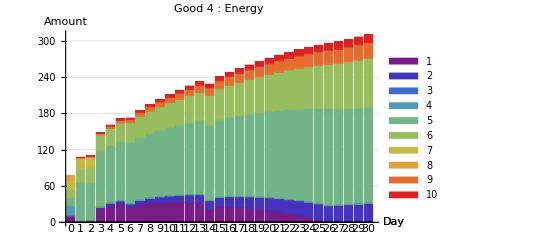
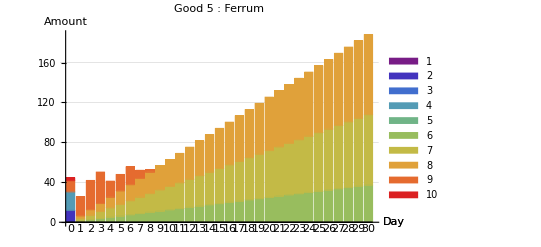

[pn]: Shows total (pn)-good storage dynamics

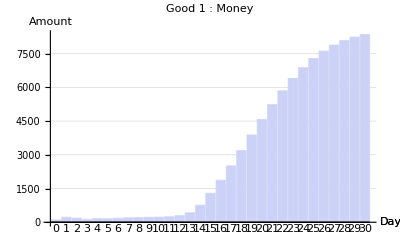
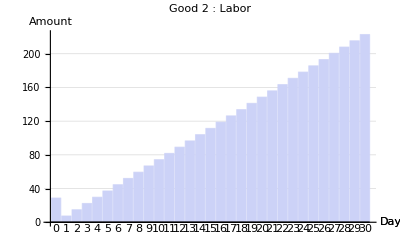
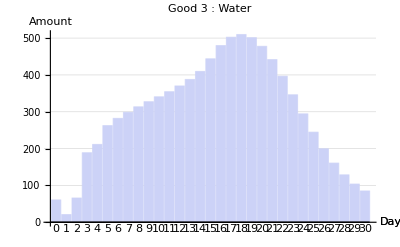
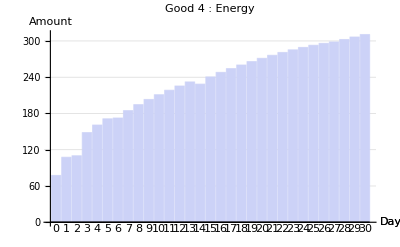
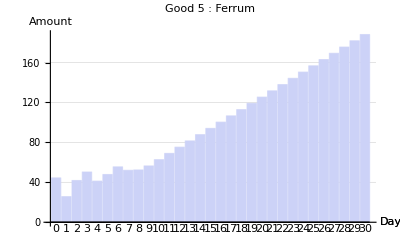

```mathematica
?MAEVisProducePart
MAEVisProducePart/@productsNums
?MAEVisConsumePart
MAEVisConsumePart/@productsNums

?MAEVisDailyProduce
MAEVisDailyProduce/@productsNums
?MAEVisDailyConsume
MAEVisDailyConsume/@productsNums

?MAEVisAverageProduce
MAEVisAverageProduce/@productsNums
?MAEVisAverageConsume
MAEVisAverageConsume/@productsNums

?MAEVisTotalProduction
MAEVisTotalProduction/@productsNums
?MAEVisTotalConsumption
MAEVisTotalConsumption/@productsNums

?MAEVisGoodStorage
MAEVisGoodStorage/@productsNums
?MAEVisTotalStorage
MAEVisTotalStorage/@ productsNums
```

[pn]: Shows amount of consumers of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows daily production of (pn)-good

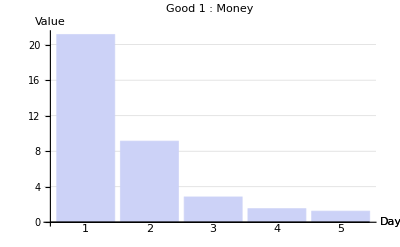
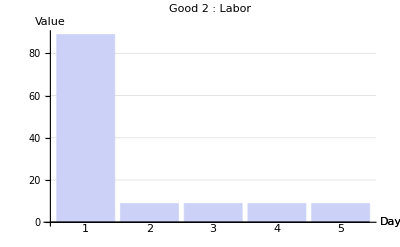
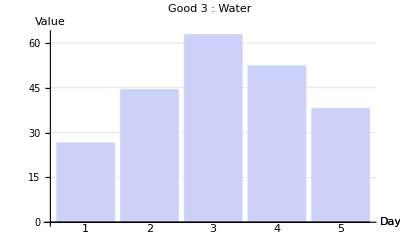
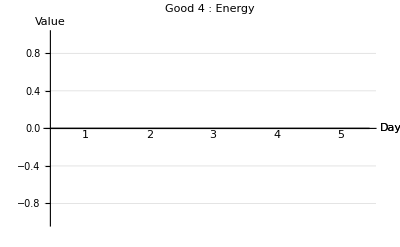
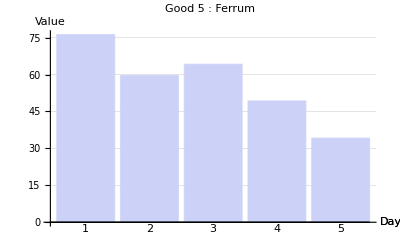

[pn]: Shows daily consumption of (pn)-good

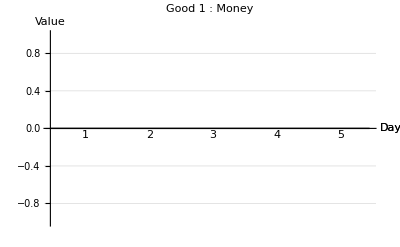
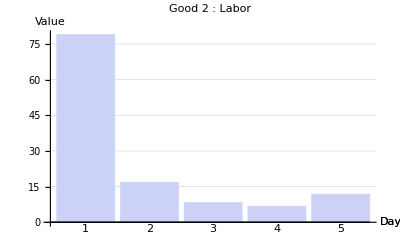
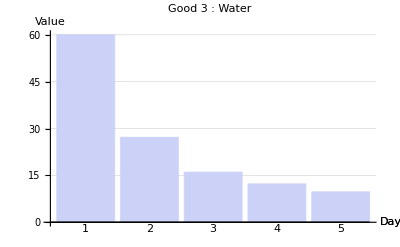
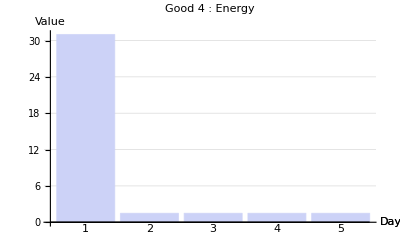
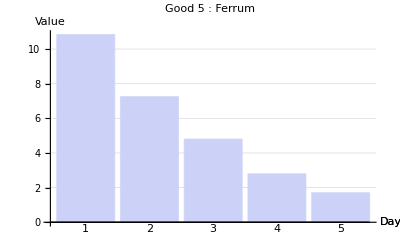

[pn]: Shows average production of (pn)-good (total prod a day / prod agents number)

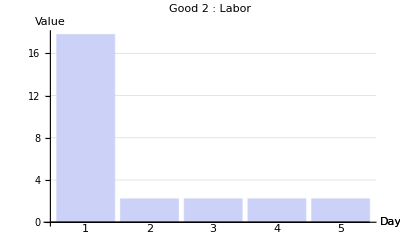
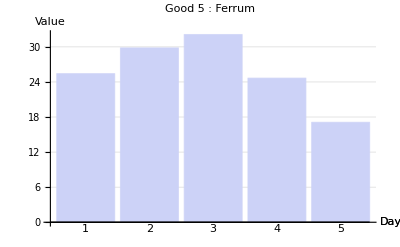
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows average consumption of (pn)-good (total cons a day / cons agents number)

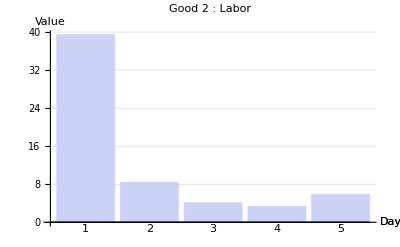
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows cumulative production of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows cumulative consumption of (pn)-good

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows (pn)-good storage dynamics by agents

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[pn]: Shows total (pn)-good storage dynamics

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,c-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

## Markets

```mathematica
<<MultiAgent`
```

```mathematica
markets/@marketsNums //MatrixForm
```

(Title→Mon/Lab | G1→1 | G2→2 | SessionsInDay→2 | FirstPrice→{1,2}
Title→Mon/Wat | G1→1 | G2→3 | SessionsInDay→2 | FirstPrice→{1,2}
Title→Mon/Ene | G1→1 | G2→4 | SessionsInDay→2 | FirstPrice→{1,2}
Title→Mon/Fer | G1→1 | G2→5 | SessionsInDay→2 | FirstPrice→{1,2})

```mathematica
hMarketsBooks[[1,2,2]]
```

{{},{{2.81528,5.53319,Bid,2,69},{3.38358,5.86107,Bid,3,70},{1.62429,5.764,Bid,7,77},{1.81287,5.75746,Bid,8,80},{1.18098,5.5551,Bid,9,83}}}

```mathematica
?MAEVisMarketBook
mn = 1;
dn=1;
sn=1;
MAEVisMarketBook[mn, dn, sn]
MAEVisMarketBooksAll[mn];
```

[mn, dn, sn]: Shows (mn)-market book in the (dn)-day before (sn)-session start

-Graphics-

```mathematica
?MAEVisMarketAuction
mn = 4;
dn=13;
sn=1;
MAEVisMarketAuction[mn, dn, sn]
```

[mn, dn, sn]: Shows double auction picture

-Graphics-

```mathematica
?MAEVisPricePrognose
an=1;
mn = 2;
MAEVisPricePrognose[an, 1, 5];
MAEVisPricePrognose[an, mn]
MAEVisPricePrognose[#,mn ]&/@agentsNums
```

[an, mn] or [an, g1, g2]: Shows price dynamics with prognoses of [an]-agent

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
<<MultiAgent`
```

```mathematica
?MAEVisMarketVolume
MAEVisMarketVolume[2]
MAEVisMarketVolume /@ marketsNums

?MAEVisAllMarketVolume
MAEVisAllMarketVolume[]

?MAEVisMarketOrdersSize
MAEVisMarketOrdersSize[2]
MAEVisMarketOrdersSize /@ marketsNums

?MAEVisAllMarketOrdersSize
MAEVisAllMarketOrdersSize[]

?MAEVisMarketDealsSize
MAEVisMarketDealsSize[2]
MAEVisMarketDealsSize /@ marketsNums

?MAEVisAllMarketDealsSize
MAEVisAllMarketDealsSize[]
```

[mn]: Shows (mn)-market volume by day/session

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[]: Shows total markets volume by day/session

-Graphics-

[mn]: Shows (mn)-market ask/bid orders amounts by day/session

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[]: Shows total ask/bid orders amounts by day/session

-Graphics-

[mn]: Shows (mn)-market deals amounts by day/session

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

[]: Shows total orders amounts by day/session

-Graphics-

```mathematica
hMarketsDeals[[4,1,1]]
```

{{1,{-16.8012,2.63091}},{4,{16.8012,-2.63091}}}

```mathematica
?MAEVisMarketDealsTable
Column@(MAEVisMarketDealsTable /@ marketsNums)
```

[mn]: Table of deals on (mn)-market

DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | [S]52.95Lab/54.10Mon | [B]11.21Lab/11.46Mon | --- | [B]5.18Lab/5.29Mon | --- | [B]22.77Lab/23.27Mon | --- | [B]9.90Lab/10.11Mon | [B]3.89Lab/3.98Mon | 0
1/2 | --- | [S]7.39Lab/7.51Mon | [B]0.66Lab/0.67Mon | [S]14.74Lab/14.99Mon | [B]2.89Lab/2.94Mon | --- | [B]5.69Lab/5.79Mon | [S]8.35Lab/8.49Mon | [B]19.96Lab/20.29Mon | [B]1.29Lab/1.31Mon | 0
2/1 | --- | [S]23.91Lab/23.18Mon | [B]5.17Lab/5.01Mon | --- | [B]12.09Lab/11.72Mon | --- | [B]2.00Lab/1.94Mon | --- | [B]4.57Lab/4.43Mon | [B]0.07Lab/0.07Mon | 0
2/2 | --- | [S]32.49Lab/31.16Mon | [B]0.31Lab/0.30Mon | --- | [B]1.40Lab/1.34Mon | --- | [B]22.54Lab/21.61Mon | --- | [B]7.89Lab/7.57Mon | [B]0.34Lab/0.33Mon | 0
3/1 | --- | [S]20.68Lab/19.34Mon | [B]2.35Lab/2.20Mon | --- | [B]1.44Lab/1.34Mon | --- | [B]2.07Lab/1.94Mon | --- | [B]14.45Lab/13.51Mon | [B]0.37Lab/0.35Mon | 0
3/2 | --- | [S]23.85Lab/22.14Mon | [B]0.11Lab/0.10Mon | --- | [B]1.16Lab/1.07Mon | --- | [B]19.88Lab/18.45Mon | --- | [B]2.67Lab/2.48Mon | [B]0.04Lab/0.03Mon | 0
4/1 | --- | --- | [B]1.12Lab/1.01Mon | --- | [B]1.34Lab/1.21Mon | --- | [B]2.15Lab/1.94Mon | [S]14.75Lab/13.32Mon | [B]10.12Lab/9.14Mon | [B]0.03Lab/0.03Mon | 0
4/2 | --- | [S]3.66Lab/3.31Mon | [B]0.05Lab/0.05Mon | [S]1.37Lab/1.24Mon | [B]1.08Lab/0.98Mon | --- | [B]18.21Lab/16.49Mon | [S]20.58Lab/18.63Mon | [B]6.26Lab/5.67Mon | [B]0.00Lab/0.00Mon | 0
5/1 | --- | [S]5.05Lab/4.44Mon | [B]0.58Lab/0.51Mon | [S]0.46Lab/0.40Mon | [B]1.28Lab/1.13Mon | --- | [B]2.21Lab/1.95Mon | [S]2.74Lab/2.41Mon | [B]4.17Lab/3.66Mon | [B]0.00Lab/0.00Mon | 0
5/2 | --- | [S]20.95Lab/18.39Mon | [B]0.03Lab/0.02Mon | --- | [B]1.04Lab/0.92Mon | --- | [B]17.21Lab/15.10Mon | --- | [B]2.67Lab/2.35Mon | --- | 0 
Market 1: Mon/Lab
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | --- | --- | --- | [B]9.00Wat/11.49Mon | [S]35.96Wat/45.92Mon | --- | [B]1.54Wat/1.97Mon | [B]7.27Wat/9.29Mon | [B]18.14Wat/23.17Mon | 0
1/2 | --- | --- | --- | --- | [B]5.02Wat/6.70Mon | --- | [S]20.55Wat/27.42Mon | --- | [B]9.53Wat/12.72Mon | [B]5.99Wat/8.00Mon | 0
2/1 | --- | --- | --- | --- | [B]19.93Wat/25.22Mon | [S]0.21Wat/0.27Mon | [S]23.61Wat/29.88Mon | --- | [B]3.55Wat/4.49Mon | [B]0.35Wat/0.44Mon | 0
2/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
3/1 | --- | --- | --- | [B]8.11Wat/9.91Mon | --- | [S]0.21Wat/0.26Mon | [S]20.73Wat/25.33Mon | --- | [B]11.15Wat/13.62Mon | [B]1.69Wat/2.07Mon | 0
3/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
4/1 | --- | --- | --- | [B]17.95Wat/21.29Mon | --- | [S]0.21Wat/0.25Mon | [S]18.83Wat/22.33Mon | [B]0.95Wat/1.12Mon | --- | [B]0.15Wat/0.17Mon | 0
4/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
5/1 | --- | --- | --- | [B]1.98Wat/2.28Mon | --- | [S]0.21Wat/0.25Mon | [S]17.66Wat/20.38Mon | [B]15.88Wat/18.33Mon | --- | [B]0.01Wat/0.02Mon | 0
5/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0 
Market 2: Mon/Wat
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | --- | --- | --- | --- | [S]5.34Ene/8.86Mon | [B]9.65Ene/16.01Mon | --- | --- | --- | [S]4.31Ene/7.15Mon | 0
1/2 | [S]2.53Ene/4.17Mon | --- | --- | --- | [S]24.35Ene/40.18Mon | [B]26.88Ene/44.34Mon | --- | --- | --- | --- | 0
2/1 | --- | --- | --- | --- | --- | [B]1.61Ene/2.53Mon | --- | --- | --- | [S]1.61Ene/2.53Mon | 0
2/2 | --- | --- | --- | --- | --- | [B]0.28Ene/0.43Mon | --- | --- | --- | [S]0.28Ene/0.43Mon | 0
3/1 | --- | --- | --- | --- | [S]0.28Ene/0.42Mon | [B]0.28Ene/0.42Mon | --- | --- | --- | --- | 0
3/2 | --- | --- | --- | --- | [S]0.18Ene/0.27Mon | [B]0.18Ene/0.27Mon | --- | --- | --- | --- | 0
4/1 | --- | --- | --- | --- | [S]0.27Ene/0.39Mon | [B]0.27Ene/0.39Mon | --- | --- | --- | --- | 0
4/2 | --- | --- | --- | --- | [S]0.18Ene/0.26Mon | [B]0.18Ene/0.26Mon | --- | --- | --- | --- | 0
5/1 | --- | --- | --- | --- | [S]0.27Ene/0.39Mon | [B]0.27Ene/0.39Mon | --- | --- | --- | --- | 0
5/2 | --- | --- | --- | --- | [S]0.18Ene/0.26Mon | [B]0.18Ene/0.26Mon | --- | --- | --- | --- | 0 
Market 3: Mon/Ene
DAY/SES | a.1 | a.2 | a.3 | a.4 | a.5 | a.6 | a.7 | a.8 | a.9 | a.10 | Σ
1/1 | [B]11.15Fer/20.98Mon | --- | [B]10.15Fer/19.09Mon | --- | --- | --- | --- | --- | [S]21.30Fer/40.07Mon | --- | 0
1/2 | --- | --- | --- | --- | --- | --- | --- | --- | --- | --- | 0
2/1 | [B]3.75Fer/6.71Mon | --- | [B]5.05Fer/9.03Mon | --- | --- | --- | --- | --- | [S]8.80Fer/15.74Mon | --- | 0
2/2 | [B]0.19Fer/0.33Mon | [B]10.00Fer/17.50Mon | [B]0.30Fer/0.53Mon | --- | --- | --- | --- | --- | [S]10.49Fer/18.36Mon | --- | 0
3/1 | [B]0.01Fer/0.02Mon | --- | [B]2.34Fer/3.99Mon | --- | --- | --- | --- | --- | [S]2.35Fer/4.01Mon | --- | 0
3/2 | [B]0.00Fer/0.00Mon | [B]8.76Fer/14.81Mon | [B]0.11Fer/0.18Mon | --- | --- | --- | --- | --- | [S]8.87Fer/15.00Mon | --- | 0
4/1 | --- | --- | [B]1.12Fer/1.83Mon | --- | --- | --- | --- | --- | [S]1.12Fer/1.83Mon | --- | 0
4/2 | --- | --- | [B]0.05Fer/0.08Mon | --- | --- | --- | --- | --- | [S]0.05Fer/0.08Mon | --- | 0
5/1 | --- | --- | [B]0.59Fer/0.92Mon | --- | --- | --- | --- | --- | [S]0.59Fer/0.92Mon | --- | 0
5/2 | --- | [B]2.20Fer/3.43Mon | [B]0.03Fer/0.04Mon | --- | --- | --- | --- | --- | [S]2.23Fer/3.47Mon | --- | 0 
Market 4: Mon/Fer

## Slide

```mathematica
<<MultiAgent`
```

```mathematica
?MAEVisAgentsHistogram
MAEVisAgentsHistogram[6]
```

[bn]: Shows histogram of agents' richness with (bn) beans